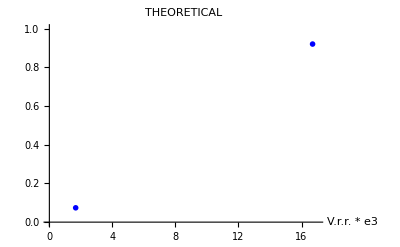

```mathematica
PlotTheoretical=ListPlot[{{1.67, 0.074},{16.7, 0.92}}, 
PlotStyle->Blue,
PlotMarkers->{{●,10}},PlotRange->{{0,17},{0,1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"THEORETICAL"]
```

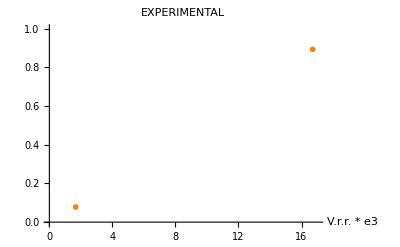

```mathematica
PlotExperimental=ListPlot[{{1.67, 78/1000},{16.7, 893/1000}}, 
PlotStyle->Orange,
PlotMarkers->{{●,10}},PlotRange->{{0,17},{0,1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"EXPERIMENTAL"]
```

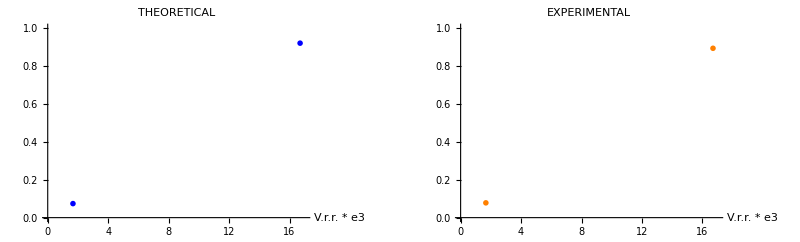

```mathematica
GraphicsRow[{PlotTheoretical, PlotExperimental}]
```